```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/fluc_T/plot/QCD

```mathematica
mub={0,100,200,300,400,500};
chi1=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi1.dat"]],{i,1,Length[mub]}];
chi2=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi2.dat"]],{i,1,Length[mub]}];
chi3=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi3.dat"]],{i,1,Length[mub]}];
chi4=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi4.dat"]],{i,1,Length[mub]}];
chi5=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi5.dat"]],{i,1,Length[mub]}];
chi6=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi6.dat"]],{i,1,Length[mub]}];
T=Flatten[Table[10+2(i),{i,1,125}]];
c1=chi1;
c2=Table[T^2(1/chi2[[i]])^1,{i,1,Length[mub]}];
c3=Table[-T^5(1/chi2[[i]])^3(chi3[[i]]),{i,1,Length[mub]}];
c4=Table[T^8(3(1/chi2[[i]])^5(chi3[[i]])^2-(1/chi2[[i]])^4 chi4[[i]]),{i,1,Length[mub]}];
c5=Table[T^11(-15(1/chi2[[i]])^7(chi3[[i]])^3-(1/chi2[[i]])^5 chi5[[i]]+10(1/chi2[[i]])^6 chi3[[i]] chi4[[i]]),{i,1,Length[mub]}];
c6=Table[T^14(105(1/chi2[[i]])^9 chi3[[i]]^4-105(1/chi2[[i]])^8 chi3[[i]]^2 chi4[[i]]+10(1/chi2[[i]])^7 chi4[[i]]^2+15(1/chi2[[i]])^7 chi3[[i]] chi5[[i]]-(1/chi2[[i]])^6 chi6[[i]]),{i,1,Length[mub]}];
Table[Export["./MUB"<>ToString[mub[[i]]]<>"/data/c2.dat",c2[[i]]],{i,1,Length[mub]}];
Table[Export["./MUB"<>ToString[mub[[i]]]<>"/data/c3.dat",c3[[i]]],{i,1,Length[mub]}];
Table[Export["./MUB"<>ToString[mub[[i]]]<>"/data/c4.dat",c4[[i]]],{i,1,Length[mub]}];
Table[Export["./MUB"<>ToString[mub[[i]]]<>"/data/c5.dat",c5[[i]]],{i,1,Length[mub]}];
Table[Export["./MUB"<>ToString[mub[[i]]]<>"/data/c6.dat",c6[[i]]],{i,1,Length[mub]}];
```

```mathematica
T
```

{12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200,202,204,206,208,210,212,214,216,218,220,222,224,226,228,230,232,234,236,238,240,242,244,246,248,250,252,254,256,258,260}

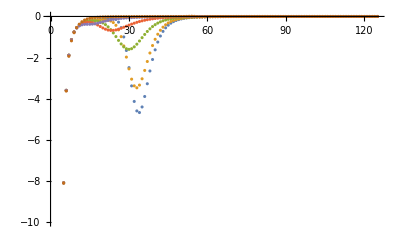

```mathematica
ListPlot[c3,PlotRange->{All,{-10,0}}]
```